```mathematica
generateKeyWithPlot[seed_Integer]:=Module[{G=4 π^2,conv=1/(1.496*^8*365.25*24*3600),pos1,vel1,pos2,vel2,pos3,vel3,q2x,q2y,q3x,q3y,m1=1,m2=1,m3=1,eq,init,sol,traj1,traj2,traj3,timeSteps,positions,keyData,binaryKeyData,flattenedBinaryKey,randomSequence,key},
(*Initial conditions*)
pos1={0,0};
vel1={0,10}*conv;
SeedRandom[seed];
q2x=RandomReal[{5,20}];q2y=RandomReal[{0,10}];
pos2={q2x,q2y};vel2={-10,0}*conv;
q3x=RandomReal[{-10,0}];q3y=RandomReal[{5,20}];
pos3={q3x,q3y};vel3={0,0};

(*Differential equations*)eq={
x1''[t]==G m2 (x2[t]-x1[t])/Norm[{x2[t]-x1[t],y2[t]-y1[t]}]^3+G m3 (x3[t]-x1[t])/Norm[{x3[t]-x1[t],y3[t]-y1[t]}]^3,y1''[t]==G m2 (y2[t]-y1[t])/Norm[{x2[t]-x1[t],y2[t]-y1[t]}]^3+G m3 (y3[t]-y1[t])/Norm[{x3[t]-x1[t],y3[t]-y1[t]}]^3,x2''[t]==G m1 (x1[t]-x2[t])/Norm[{x1[t]-x2[t],y1[t]-y2[t]}]^3+G m3 (x3[t]-x2[t])/Norm[{x3[t]-x2[t],y3[t]-y2[t]}]^3,y2''[t]==G m1 (y1[t]-y2[t])/Norm[{x1[t]-x2[t],y1[t]-y2[t]}]^3+G m3 (y3[t]-y2[t])/Norm[{x3[t]-x2[t],y3[t]-y2[t]}]^3,x3''[t]==G m1 (x1[t]-x3[t])/Norm[{x1[t]-x3[t],y1[t]-y3[t]}]^3+G m2 (x2[t]-x3[t])/Norm[{x2[t]-x3[t],y2[t]-y3[t]}]^3,y3''[t]==G m1 (y1[t]-y3[t])/Norm[{x1[t]-x3[t],y1[t]-y3[t]}]^3+G m2 (y2[t]-y3[t])/Norm[{x2[t]-x3[t],y2[t]-y3[t]}]^3};

(*Initial conditions for solver*)init={x1[0]==pos1[[1]],y1[0]==pos1[[2]],x2[0]==pos2[[1]],y2[0]==pos2[[2]],x3[0]==pos3[[1]],y3[0]==pos3[[2]],x1'[0]==vel1[[1]],y1'[0]==vel1[[2]],x2'[0]==vel2[[1]],y2'[0]==vel2[[2]],x3'[0]==vel3[[1]],y3'[0]==vel3[[2]]};

(*Solve system*)sol=NDSolve[{eq,init},{x1,y1,x2,y2,x3,y3},{t,0,100}];
(*Extract trajectories*)
traj1={x1[t],y1[t]}/. sol;
traj2={x2[t],y2[t]}/. sol;
traj3={x3[t],y3[t]}/. sol;
(*Sample positions*)timeSteps=Range[0,100,0.1];
positions=Flatten[Table[{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]}/. sol,{t,timeSteps}],1];
(*Convert to binary*)keyData=Flatten[positions];
binaryKeyData=IntegerDigits[Round[Abs[keyData]*10^6],2,24];
flattenedBinaryKey=Flatten[binaryKeyData];
(*XOR with PRBS*)randomSequence=RandomInteger[{0,1},Length[flattenedBinaryKey]];
key=BitXor[flattenedBinaryKey,randomSequence];

(*Print info*)Print["Seed: ",seed];
Print["Key length: ",Length[key]];
Print["Counts: ",Counts[key]];

(*Plot trajectories*)
initialPoints={pos1,pos2,pos3};

trajectoryPlot=ParametricPlot[{traj1,traj2,traj3},{t,0,100},PlotStyle->Automatic,Frame->True,FrameStyle->Directive[Black,Thin],FrameLabel->{Style["x (au)",Italic,14],Style["y (au)",Italic,14]},PlotRange->{{-10,10},{-5,15}},AspectRatio->1,AxesOrigin->{0,0},ImageSize->500,PlotLegends->Placed[LineLegend[ {"Particle 1","Particle 2","Particle 3"},LegendMarkerSize->10,LegendFunction->(Framed[#,RoundingRadius->0]&)], Below],Epilog->{Black,PointSize[Large],Point[initialPoints]}];

Print[trajectoryPlot];

(*Return key*)
key]
```

Seed: 67

Key length: 144144

Counts: <|0→71613,1→72531|>

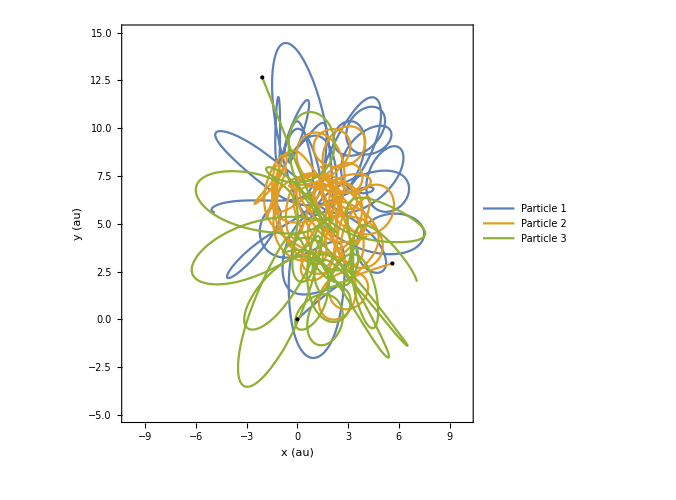

Seed: 12

Key length: 144144

Counts: <|0→71829,1→72315|>

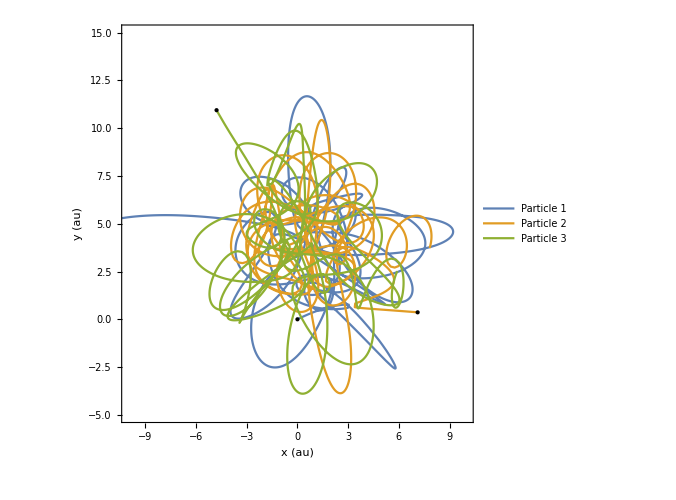

XOR key length: 144144

XOR key counts: <|0→71768,1→72376|>

```mathematica
key1=generateKeyWithPlot[67];
key2=generateKeyWithPlot[12];

len=Min[Length[key1],Length[key2]];
key=BitXor[key1[[;;len]],key2[[;;len]]];

Print["XOR key length: ",len];
Print["XOR key counts: ",Counts[key]];
```

```mathematica
(*SerialRandomnessTest*)
serialResult=N@ResourceFunction["SerialRandomnessTest"][key,"TestStatistic"];
serialPValue=N@ResourceFunction["SerialRandomnessTest"][key,"PValue"];
Print["Serial Randomness Test:"];
Print["  Test Statistic: ",serialResult];
Print["  P-Value: ",serialPValue];
If[serialPValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*ChiSquareRandomnessTest*)
chiSquareResult=N@ResourceFunction["ChiSquareRandomnessTest"][key,"TestStatistic"];
chiSquarePValue=N@ResourceFunction["ChiSquareRandomnessTest"][key,"PValue"];
Print["\nChi-Square Randomness Test:"];
Print["  Test Statistic: ",chiSquareResult];
Print["  P-Value: ",chiSquarePValue];
If[chiSquarePValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*BinaryRunRandomnessTest*)
binaryRunResult=N@ResourceFunction["BinaryRunRandomnessTest"][key,"TestStatistic"];
binaryRunPValue=N@ResourceFunction["BinaryRunRandomnessTest"][key,"PValue"];
Print["\nBinary Run Randomness Test:"];
Print["  Test Statistic: ",binaryRunResult];
Print["  P-Value: ",binaryRunPValue];
If[binaryRunPValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*ArcsineLawRandomnessTest*)
arcsineResult=N@ResourceFunction["ArcsineLawRandomnessTest"][key,"TestStatistic"];
arcsinePValue=N@ResourceFunction["ArcsineLawRandomnessTest"][key,"PValue"]; (*Force numeric evaluation*)
Print["\nArcsine Law Randomness Test:"];
Print["  Test Statistic: ",arcsineResult];
Print["  P-Value: ",arcsinePValue];
If[arcsinePValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];
```

Serial Randomness Test:

Test Statistic: 0.841303

P-Value: 0.643647

Result: Good randomness (p-value > 0.05)

Chi-Square Randomness Test:

Test Statistic: 0.44758

P-Value: 0.503486

Result: Good randomness (p-value > 0.05)

Binary Run Randomness Test:

Test Statistic: 71950.

P-Value: 0.521199

Result: Good randomness (p-value > 0.05)

Arcsine Law Randomness Test:

Test Statistic: 0.414259

P-Value: 0.890289

Serial Randomness Test:

Test Statistic: 2.04372

P-Value: 0.317225

Result: Good randomness (p-value > 0.05)

Chi-Square Randomness Test:

Test Statistic: 2.56455

P-Value: 0.109284

Result: Good randomness (p-value > 0.05)

Binary Run Randomness Test:

Test Statistic: 72099.

P-Value: 0.881562

Result: Good randomness (p-value > 0.05)

Arcsine Law Randomness Test:

Test Statistic: 0.884928

P-Value: 0.440657

Result: Good randomness (p-value > 0.05)

Result: Good randomness (p-value > 0.05)

```mathematica
generateSBoxFromKey[key_List]:=Module[{chunks,values,sbox,plot},(*1. Partition into 8-bit blocks*)chunks=Partition[key,8];
(*2. Convert each block to decimal*)values=FromDigits[#,2]&/@chunks;
(*3. Extract first 256 unique values*)sbox=DeleteDuplicates[values];
sbox=Take[sbox,256];
(*4. Check length*)If[Length[sbox]<256,Print["⚠️ Not enough unique values to form a full S-box!"];
Return[$Failed];];
(*5. Print S-box*)Print["✅ S-box generated (length = ",Length[sbox],"):"];
Print[sbox];
(*6. Visualize as 16×16 grid*)plot=ArrayPlot[Partition[sbox,16],ColorFunction->"Rainbow",Frame->True,Mesh->True,PlotLabel->"S-box Visualization",ImageSize->Large];
Print[plot];
(*7. Return S-box*)sbox];
```

✅ S-box generated (length = 256):

{82,49,190,65,185,102,7,143,73,153,127,218,187,99,63,140,253,96,192,34,130,150,248,132,194,199,39,176,45,216,133,36,72,17,6,204,129,31,242,160,210,215,120,93,254,61,35,183,24,231,196,91,121,189,128,206,229,201,69,245,88,112,107,74,83,131,75,174,221,67,14,205,220,197,226,27,249,71,118,78,56,105,151,200,8,122,152,135,195,18,30,19,85,11,21,66,16,46,233,149,5,179,15,54,70,147,224,162,37,51,239,20,80,101,188,9,148,164,161,225,138,64,234,208,235,68,111,119,255,0,113,26,139,240,214,10,168,203,25,178,166,169,100,1,12,145,29,142,33,97,59,84,4,146,191,137,159,250,237,238,211,38,110,227,232,28,47,77,115,79,171,167,202,247,157,241,114,87,98,43,50,13,23,134,126,170,228,173,3,124,117,94,55,53,106,89,163,40,212,32,207,62,158,213,57,184,76,243,60,181,22,92,109,90,182,209,141,219,180,198,86,108,223,172,177,125,123,252,156,81,165,175,155,222,58,52,44,230,154,244,95,251,104,193,186,103,41,42,116,246,136,144,217,48,2,236}

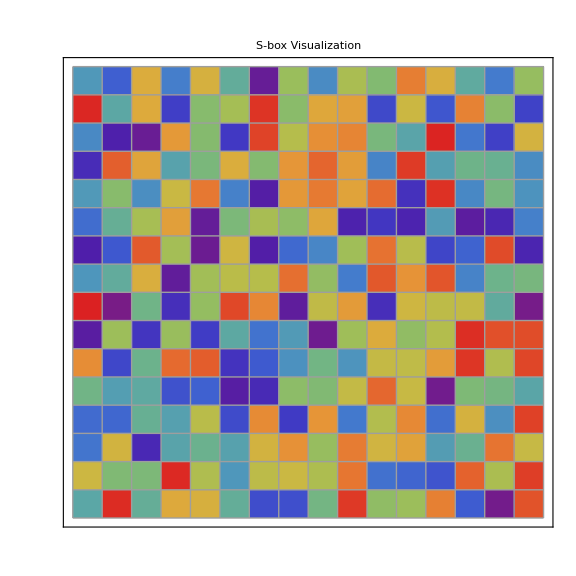

✅ S-box generated (length = 256):

{204,41,147,243,84,53,51,81,249,174,142,228,82,145,223,202,158,80,156,59,89,39,125,171,172,239,217,32,118,17,40,235,90,85,12,236,209,149,141,72,96,140,192,128,182,224,124,144,45,250,226,203,115,180,44,121,185,30,177,219,189,87,179,127,151,242,164,61,77,199,100,150,35,67,229,70,245,184,66,116,216,94,92,207,18,136,232,161,119,187,107,68,193,191,95,93,14,186,5,129,152,108,13,241,83,10,251,133,237,248,159,34,210,153,76,64,4,27,113,43,9,19,165,42,3,170,208,7,197,28,101,36,75,47,162,0,123,160,247,190,106,178,215,205,134,98,221,175,46,65,62,49,52,246,102,21,25,103,138,233,139,86,240,206,71,122,167,230,74,56,11,114,220,196,91,200,79,183,176,238,104,169,23,73,111,16,168,146,157,110,155,109,201,50,231,24,57,48,214,33,194,198,166,132,234,130,173,29,195,88,20,112,31,244,163,211,6,255,225,137,8,181,38,227,105,117,54,252,218,148,58,60,26,22,188,97,120,143,212,2,222,78,135,253,69,15,213,37,1,131,254,154,99,63,55,126}

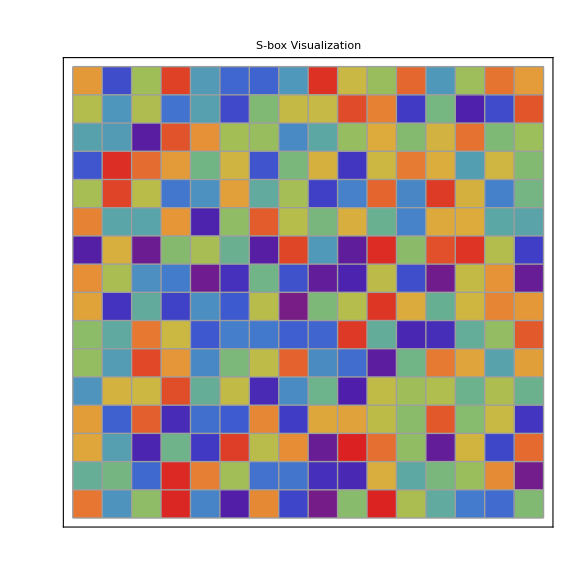

✅ S-box generated (length = 256):

{14,198,52,209,179,34,94,197,96,56,10,137,151,61,38,98,5,48,159,9,199,111,144,13,201,239,17,83,145,128,185,66,27,73,36,57,43,149,170,103,228,69,71,118,227,109,23,63,157,26,171,91,42,165,72,115,12,41,167,99,181,84,85,1,6,75,108,64,39,250,223,16,47,207,32,70,249,20,21,255,161,162,15,30,79,187,232,76,125,33,24,218,231,126,183,192,208,31,131,67,22,186,244,213,237,114,174,143,49,28,88,3,164,226,141,203,152,166,252,189,116,87,119,140,117,74,191,81,214,251,196,212,102,77,90,202,193,54,0,205,2,142,127,146,136,132,93,106,105,100,8,92,147,19,59,153,150,248,62,154,234,180,238,156,55,112,221,178,86,89,177,243,224,134,4,160,122,222,247,253,240,35,101,242,40,60,107,219,225,195,245,51,7,124,95,104,172,235,188,129,25,175,135,254,97,176,233,65,168,230,155,18,58,182,46,200,194,173,220,215,130,138,133,120,11,44,121,246,29,45,53,163,229,204,82,217,211,236,216,80,210,113,241,123,148,190,139,184,110,169,158,50,206,78,68,37}

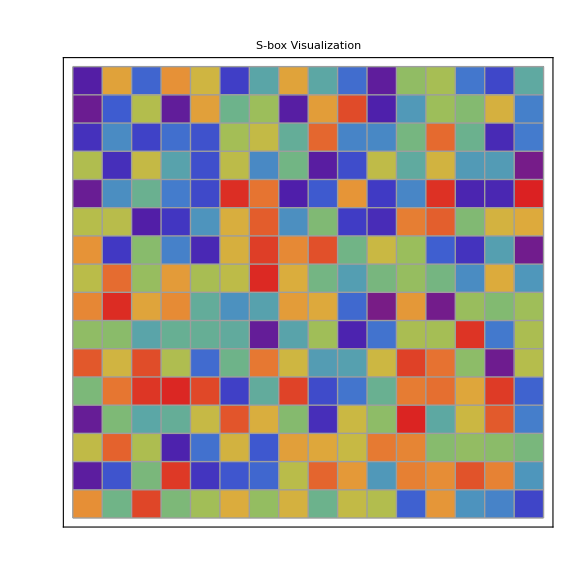

```mathematica
chunkSize=Floor[Length[key]/3];
keyParts={key[[1;;chunkSize]],key[[chunkSize+1;;2 chunkSize]],key[[2 chunkSize+1;;3 chunkSize]]};

(*Assign each S-box to a named variable*)
sbox1=generateSBoxFromKey[keyParts[[1]]];
sbox2=generateSBoxFromKey[keyParts[[2]]];
sbox3=generateSBoxFromKey[keyParts[[3]]];
```

```mathematica
ClearAll[EvalSboxWithReport]
EvalSboxWithReport[sbox_]:=Module[{sboxBitCount,sboxBitsLists,sboxBitLvlsList,NaturalBasis,walshM,nonLin,SACRes2D,calBitVal,sac,bic,lap,DifList2D,dap},(*Setup*)sboxBitCount=Log2[Length[sbox]];
sboxBitsLists=Table[IntegerDigits[sbox[[i]],2,sboxBitCount],{i,Length[sbox]}];
sboxBitLvlsList=Table[Table[sboxBitsLists[[i]][[j]],{i,Length[sbox]}],{j,sboxBitCount}];
(*Walsh matrix*)
NaturalBasis[s_]:=With[{u={{1,1},{1,-1}}},Nest[ArrayFlatten[#/. {1->u,-1->-u}]&,{{1}},s]];
walshM=NaturalBasis[sboxBitCount];
(*Nonlinearity*)
nonLin=Max[Table[2^(sboxBitCount-1)-Max[Abs[Drop[sboxBitLvlsList[[i]].walshM,1]]],{i,Length[sboxBitLvlsList]}]];
(*SAC matrix*)
SACRes2D=Table[Table[0,{i,sboxBitCount}],{j,sboxBitCount}];
calBitVal[m_,n_,testVal_]:=BitAnd[IntegerPart[testVal/(2^n)],1];

For[m=0,m<sboxBitCount,m++,For[i=0,i<=Length[sbox]-1,i++,For[n=0,n<sboxBitCount,n++,SACRes2D[[m+1]][[n+1]]+=calBitVal[m,n,BitXor[sbox[[i+1]],sbox[[BitXor[i,2^m]+1]]]]]]];
(*SAC average*)sac=Total[Total[SACRes2D/(2^sboxBitCount)]]/sboxBitCount^2;
(*BIC*)bic=2^(sboxBitCount-1)-Max[Abs[2^(sboxBitCount-1)-Flatten[SACRes2D]]];
(*LAP*)lap=Max[Abs[(Flatten[SACRes2D]/2^(sboxBitCount))-0.5]];
(*DAP*)DifList2D=Table[0,{i,(2^sboxBitCount)}];

For[i=1,i<=Length[sbox],i++,For[j=1,j<=Length[sbox],j++,DifList2D[[i]]+=((sbox[[i]]-sbox[[j]]))]];
dap=1/Mean[Abs[DifList2D/2^(sboxBitCount)]];
(*Optimal reference values*)
maxNonLin=2^(sboxBitCount-1)-2^(sboxBitCount/2-1);(*theoretical max*)idealSAC=0.5;
idealLAP=0;
idealDAP=1;

(*Print report*)
Print["Bits per entry: ",sboxBitCount];
Print["----------------------------------"];
Print["Nonlinearity: ",nonLin," (max theoretical: ",maxNonLin,")"];
Print["SAC (Strict Avalanche): ",NumberForm[N[sac],{3,2}]," (ideal: ",idealSAC,")"];
Print["BIC (Bit Independence): ",bic];
Print["LAP (Linear Approx.): ",NumberForm[N[lap],{3,2}]," (ideal: ",idealLAP,")"];
Print["DAP (Differential Approx.): ",NumberForm[N[dap],{3,2}]," (ideal: ",idealDAP,")"];
Print["----------------------------------"];
(*Return metrics as list*){nonLin,sac,bic,lap,dap}];
```

```mathematica
EvalSboxWithReport[sbox1];
EvalSboxWithReport[sbox2];
EvalSboxWithReport[sbox3];
```

Bits per entry: 8

----------------------------------

Nonlinearity: 108 (max theoretical: 120)

SAC (Strict Avalanche): 0.50 (ideal: 0.5)

BIC (Bit Independence): 104

LAP (Linear Approx.): 0.09 (ideal: 0)

DAP (Differential Approx.): 0.02 (ideal: 1)

----------------------------------

Bits per entry: 8

----------------------------------

Nonlinearity: 106 (max theoretical: 120)

SAC (Strict Avalanche): 0.50 (ideal: 0.5)

BIC (Bit Independence): 84

LAP (Linear Approx.): 0.17 (ideal: 0)

DAP (Differential Approx.): 0.02 (ideal: 1)

----------------------------------

Bits per entry: 8

----------------------------------

Nonlinearity: 106 (max theoretical: 120)

SAC (Strict Avalanche): 0.50 (ideal: 0.5)

BIC (Bit Independence): 96

LAP (Linear Approx.): 0.13 (ideal: 0)

DAP (Differential Approx.): 0.02 (ideal: 1)

----------------------------------